```mathematica
Series[(Exp[1/2I π(σ1-σ2)^2]Exp[1/2I π(σ1-σ3)^2]Exp[1/2I π(σ2-σ3)^2]Exp[1/2I π(σ3)^2]Exp[1/2I π(σ2)^2]Exp[1/2I π(σ1)^2]Exp[1/2I π(σ1+σ2)^2]Exp[1/2I π(σ1+σ3)^2]Exp[1/2I π(σ2+σ3)^2])/(BarnesG[1-σ1+σ2]BarnesG[1+σ1-σ2]BarnesG[1-σ1+σ3]BarnesG[1+σ1-σ3]BarnesG[1-σ2+σ3]BarnesG[1+σ2-σ3]BarnesG[1-σ3]BarnesG[1+σ3]BarnesG[1-σ2]BarnesG[1+σ2]BarnesG[1-σ1]BarnesG[1+σ1]BarnesG[1-σ1-σ2]BarnesG[1+σ1+σ2]BarnesG[1-σ1-σ3]BarnesG[1+σ1+σ3]BarnesG[1-σ2-σ3]BarnesG[1+σ2+σ3]),{σ1,Infinity,0},{σ2,Infinity,0},{σ3,Infinity,0}]
```

$Aborted

```mathematica
Exp[1/2I π(σ1-σ2)^2]Exp[1/2I π(σ1-σ3)^2]Exp[1/2I π(σ2-σ3)^2]Exp[1/2I π(σ1+σ2)^2]Exp[1/2I π(σ1+σ3)^2]Exp[1/2I π(σ2+σ3)^2]//Simplify
```

ⅇ^(2 ⅈ π (σ1^2+σ2^2+σ3^2))

```mathematica
(*B_3*)
```

```mathematica
Simplify[(4 (σ3^2 Subscript[F, 0][σ1,σ2,-1+σ3] Subscript[F, 0][σ1,σ2,1+σ3]+σ2^2 Subscript[F, 0][σ1,-1+σ2,σ3] Subscript[F, 0][σ1,1+σ2,σ3]+σ1^2 Subscript[F, 0][-1+σ1,σ2,σ3] Subscript[F, 0][1+σ1,σ2,σ3]))/(Subscript[F, 0][σ1,σ2,σ3])^2/. Subscript[F, 0][σ1_,σ2_,σ3_]->(Exp[1/2I π(σ1-σ2)^2]Exp[1/2I π(σ1-σ3)^2]Exp[1/2I π(σ2-σ3)^2]Exp[1/2I π(σ3)^2]Exp[1/2I π(σ2)^2]Exp[1/2I π(σ1)^2]Exp[1/2I π(σ1+σ2)^2]Exp[1/2I π(σ1+σ3)^2]Exp[1/2I π(σ2+σ3)^2])/(G[1-σ1+σ2]G[1+σ1-σ2]G[1-σ1+σ3]G[1+σ1-σ3]G[1-σ2+σ3]G[1+σ2-σ3]G[1-σ3]G[1+σ3]G[1-σ2]G[1+σ2]G[1-σ1]G[1+σ1]G[1-σ1-σ2]G[1+σ1+σ2]G[1-σ1-σ3]G[1+σ1+σ3]G[1-σ2-σ3]G[1+σ2+σ3]),{σ1 >0, σ2 >0, σ3 >0,σ4>0}]
```

(8 (σ1^4+σ2^4-σ2^2 σ3^2+σ3^4-σ1^2 (σ2^2+σ3^2)))/((σ1-σ2)^2 (σ1+σ2)^2 (σ1-σ3)^2 (σ2-σ3)^2 (σ1+σ3)^2 (σ2+σ3)^2)

```mathematica
(Simplify[-1/(4 (Subscript[F, 0][σ1,σ2,σ3])^2)(-((8 (σ1^4+σ2^4-σ1^2 (σ2^2+(-1+σ3)^2)-σ2^2 (-1+σ3)^2+(-1+σ3)^4) (1-2 σ3)^2)/((σ1-σ2)^2 (σ1+σ2)^2 (1+σ1-σ3)^2 (1+σ2-σ3)^2 (-1+σ1+σ3)^2 (-1+σ2+σ3)^2)+(8 (1+2 σ3)^2 (σ1^4+σ2^4-σ2^2 (1+σ3)^2+(1+σ3)^4-σ1^2 (σ2^2+(1+σ3)^2)))/((σ1-σ2)^2 (σ1+σ2)^2 (-1+σ1-σ3)^2 (-1+σ2-σ3)^2 (1+σ1+σ3)^2 (1+σ2+σ3)^2)) Subscript[F, 0][σ1,σ2,-1+σ3] Subscript[F, 0][σ1,σ2,1+σ3]+4 (σ2-σ3)^2 Subscript[F, 0][σ1,-1+σ2,1+σ3] Subscript[F, 0][σ1,1+σ2,-1+σ3]-((8 (1-2 σ2)^2 (σ1^4+(-1+σ2)^4-(-1+σ2)^2 σ3^2+σ3^4-σ1^2 ((-1+σ2)^2+σ3^2)))/((1+σ1-σ2)^2 (-1+σ1+σ2)^2 (σ1-σ3)^2 (-1+σ2-σ3)^2 (σ1+σ3)^2 (-1+σ2+σ3)^2)+(8 (1+2 σ2)^2 (σ1^4+(1+σ2)^4-(1+σ2)^2 σ3^2+σ3^4-σ1^2 ((1+σ2)^2+σ3^2)))/((-1+σ1-σ2)^2 (1+σ1+σ2)^2 (σ1-σ3)^2 (1+σ2-σ3)^2 (σ1+σ3)^2 (1+σ2+σ3)^2)) Subscript[F, 0][σ1,-1+σ2,σ3] Subscript[F, 0][σ1,1+σ2,σ3]+4 (σ2+σ3)^2 Subscript[F, 0][σ1,-1+σ2,-1+σ3] Subscript[F, 0][σ1,1+σ2,1+σ3]+4 σ1^2 Subscript[F, 0][-1+σ1,1+σ2,σ3] Subscript[F, 0][1+σ1,-1+σ2,σ3]-8 σ1 σ2 Subscript[F, 0][-1+σ1,1+σ2,σ3] Subscript[F, 0][1+σ1,-1+σ2,σ3]+4 σ2^2 Subscript[F, 0][-1+σ1,1+σ2,σ3] Subscript[F, 0][1+σ1,-1+σ2,σ3]+4 σ1^2 Subscript[F, 0][-1+σ1,σ2,1+σ3] Subscript[F, 0][1+σ1,σ2,-1+σ3]-8 σ1 σ3 Subscript[F, 0][-1+σ1,σ2,1+σ3] Subscript[F, 0][1+σ1,σ2,-1+σ3]+4 σ3^2 Subscript[F, 0][-1+σ1,σ2,1+σ3] Subscript[F, 0][1+σ1,σ2,-1+σ3]-((8 (1-2 σ1)^2 ((-1+σ1)^4+σ2^4-σ2^2 σ3^2+σ3^4-(-1+σ1)^2 (σ2^2+σ3^2)))/((-1+σ1-σ2)^2 (-1+σ1+σ2)^2 (-1+σ1-σ3)^2 (σ2-σ3)^2 (-1+σ1+σ3)^2 (σ2+σ3)^2)+(8 (1+2 σ1)^2 ((1+σ1)^4+σ2^4-σ2^2 σ3^2+σ3^4-(1+σ1)^2 (σ2^2+σ3^2)))/((1+σ1-σ2)^2 (1+σ1+σ2)^2 (1+σ1-σ3)^2 (σ2-σ3)^2 (1+σ1+σ3)^2 (σ2+σ3)^2)) Subscript[F, 0][-1+σ1,σ2,σ3] Subscript[F, 0][1+σ1,σ2,σ3]+4 σ1^2 Subscript[F, 0][-1+σ1,σ2,-1+σ3] Subscript[F, 0][1+σ1,σ2,1+σ3]+8 σ1 σ3 Subscript[F, 0][-1+σ1,σ2,-1+σ3] Subscript[F, 0][1+σ1,σ2,1+σ3]+4 σ3^2 Subscript[F, 0][-1+σ1,σ2,-1+σ3] Subscript[F, 0][1+σ1,σ2,1+σ3]+4 σ1^2 Subscript[F, 0][-1+σ1,-1+σ2,σ3] Subscript[F, 0][1+σ1,1+σ2,σ3]+8 σ1 σ2 Subscript[F, 0][-1+σ1,-1+σ2,σ3] Subscript[F, 0][1+σ1,1+σ2,σ3]+4 σ2^2 Subscript[F, 0][-1+σ1,-1+σ2,σ3] Subscript[F, 0][1+σ1,1+σ2,σ3])/. Subscript[F, 0][σ1_,σ2_,σ3_]->1/(G[1-σ1+σ2]^2G[1-σ1+σ3]^2G[1-σ2+σ3]^2G[1+σ3]^2G[1+σ2]^2G[1+σ1]^2G[1+σ1+σ2]^2G[1+σ1+σ3]^2G[1+σ2+σ3]^2),{σ1 >0, σ2 >0, σ3 >0,σ4>0}]//Together)-((2 (σ1^6 σ2^2-6 σ1^8 σ2^2+15 σ1^10 σ2^2-20 σ1^12 σ2^2+15 σ1^14 σ2^2-6 σ1^16 σ2^2+σ1^18 σ2^2-2 σ1^4 σ2^4+6 σ1^6 σ2^4-6 σ1^8 σ2^4+2 σ1^10 σ2^4+2 σ1^12 σ2^4-6 σ1^14 σ2^4+6 σ1^16 σ2^4-2 σ1^18 σ2^4+σ1^2 σ2^6+6 σ1^4 σ2^6-18 σ1^6 σ2^6+18 σ1^8 σ2^6-14 σ1^10 σ2^6+18 σ1^12 σ2^6-18 σ1^14 σ2^6+6 σ1^16 σ2^6+σ1^18 σ2^6-6 σ1^2 σ2^8-6 σ1^4 σ2^8+18 σ1^6 σ2^8-6 σ1^8 σ2^8-6 σ1^10 σ2^8+18 σ1^12 σ2^8-6 σ1^14 σ2^8-6 σ1^16 σ2^8+15 σ1^2 σ2^10+2 σ1^4 σ2^10-14 σ1^6 σ2^10-6 σ1^8 σ2^10-14 σ1^10 σ2^10+2 σ1^12 σ2^10+15 σ1^14 σ2^10-20 σ1^2 σ2^12+2 σ1^4 σ2^12+18 σ1^6 σ2^12+18 σ1^8 σ2^12+2 σ1^10 σ2^12-20 σ1^12 σ2^12+15 σ1^2 σ2^14-6 σ1^4 σ2^14-18 σ1^6 σ2^14-6 σ1^8 σ2^14+15 σ1^10 σ2^14-6 σ1^2 σ2^16+6 σ1^4 σ2^16+6 σ1^6 σ2^16-6 σ1^8 σ2^16+σ1^2 σ2^18-2 σ1^4 σ2^18+σ1^6 σ2^18+σ1^6 σ3^2-6 σ1^8 σ3^2+15 σ1^10 σ3^2-20 σ1^12 σ3^2+15 σ1^14 σ3^2-6 σ1^16 σ3^2+σ1^18 σ3^2+16 σ1^6 σ2^2 σ3^2-44 σ1^8 σ2^2 σ3^2+4 σ1^10 σ2^2 σ3^2+104 σ1^12 σ2^2 σ3^2-136 σ1^14 σ2^2 σ3^2+68 σ1^16 σ2^2 σ3^2-12 σ1^18 σ2^2 σ3^2-16 σ1^4 σ2^4 σ3^2-84 σ1^6 σ2^4 σ3^2+358 σ1^8 σ2^4 σ3^2-513 σ1^10 σ2^4 σ3^2+360 σ1^12 σ2^4 σ3^2-82 σ1^14 σ2^4 σ3^2-38 σ1^16 σ2^4 σ3^2+15 σ1^18 σ2^4 σ3^2+σ2^6 σ3^2+16 σ1^2 σ2^6 σ3^2-84 σ1^4 σ2^6 σ3^2+572 σ1^6 σ2^6 σ3^2-1047 σ1^8 σ2^6 σ3^2+1792 σ1^10 σ2^6 σ3^2-1590 σ1^12 σ2^6 σ3^2+844 σ1^14 σ2^6 σ3^2-200 σ1^16 σ2^6 σ3^2+16 σ1^18 σ2^6 σ3^2-6 σ2^8 σ3^2-44 σ1^2 σ2^8 σ3^2+358 σ1^4 σ2^8 σ3^2-1047 σ1^6 σ2^8 σ3^2-784 σ1^8 σ2^8 σ3^2+740 σ1^10 σ2^8 σ3^2-904 σ1^12 σ2^8 σ3^2+311 σ1^14 σ2^8 σ3^2-64 σ1^16 σ2^8 σ3^2+15 σ2^10 σ3^2+4 σ1^2 σ2^10 σ3^2-513 σ1^4 σ2^10 σ3^2+1792 σ1^6 σ2^10 σ3^2+740 σ1^8 σ2^10 σ3^2+524 σ1^10 σ2^10 σ3^2-110 σ1^12 σ2^10 σ3^2+128 σ1^14 σ2^10 σ3^2-20 σ2^12 σ3^2+104 σ1^2 σ2^12 σ3^2+360 σ1^4 σ2^12 σ3^2-1590 σ1^6 σ2^12 σ3^2-904 σ1^8 σ2^12 σ3^2-110 σ1^10 σ2^12 σ3^2-160 σ1^12 σ2^12 σ3^2+15 σ2^14 σ3^2-136 σ1^2 σ2^14 σ3^2-82 σ1^4 σ2^14 σ3^2+844 σ1^6 σ2^14 σ3^2+311 σ1^8 σ2^14 σ3^2+128 σ1^10 σ2^14 σ3^2-6 σ2^16 σ3^2+68 σ1^2 σ2^16 σ3^2-38 σ1^4 σ2^16 σ3^2-200 σ1^6 σ2^16 σ3^2-64 σ1^8 σ2^16 σ3^2+σ2^18 σ3^2-12 σ1^2 σ2^18 σ3^2+15 σ1^4 σ2^18 σ3^2+16 σ1^6 σ2^18 σ3^2-2 σ1^4 σ3^4+6 σ1^6 σ3^4-6 σ1^8 σ3^4+2 σ1^10 σ3^4+2 σ1^12 σ3^4-6 σ1^14 σ3^4+6 σ1^16 σ3^4-2 σ1^18 σ3^4-16 σ1^4 σ2^2 σ3^4-84 σ1^6 σ2^2 σ3^4+358 σ1^8 σ2^2 σ3^4-513 σ1^10 σ2^2 σ3^4+360 σ1^12 σ2^2 σ3^4-82 σ1^14 σ2^2 σ3^4-38 σ1^16 σ2^2 σ3^4+15 σ1^18 σ2^2 σ3^4-2 σ2^4 σ3^4-16 σ1^2 σ2^4 σ3^4+636 σ1^4 σ2^4 σ3^4-1292 σ1^6 σ2^4 σ3^4+1570 σ1^8 σ2^4 σ3^4-2664 σ1^10 σ2^4 σ3^4+2040 σ1^12 σ2^4 σ3^4-652 σ1^14 σ2^4 σ3^4+156 σ1^16 σ2^4 σ3^4-32 σ1^18 σ2^4 σ3^4+6 σ2^6 σ3^4-84 σ1^2 σ2^6 σ3^4-1292 σ1^4 σ2^6 σ3^4+1446 σ1^6 σ2^6 σ3^4-556 σ1^8 σ2^6 σ3^4+784 σ1^10 σ2^6 σ3^4-1050 σ1^12 σ2^6 σ3^4+122 σ1^14 σ2^6 σ3^4+64 σ1^16 σ2^6 σ3^4-6 σ2^8 σ3^4+358 σ1^2 σ2^8 σ3^4+1570 σ1^4 σ2^8 σ3^4-556 σ1^6 σ2^8 σ3^4+344 σ1^8 σ2^8 σ3^4+750 σ1^10 σ2^8 σ3^4+44 σ1^12 σ2^8 σ3^4-64 σ1^14 σ2^8 σ3^4+2 σ2^10 σ3^4-513 σ1^2 σ2^10 σ3^4-2664 σ1^4 σ2^10 σ3^4+784 σ1^6 σ2^10 σ3^4+750 σ1^8 σ2^10 σ3^4-930 σ1^10 σ2^10 σ3^4+32 σ1^12 σ2^10 σ3^4+2 σ2^12 σ3^4+360 σ1^2 σ2^12 σ3^4+2040 σ1^4 σ2^12 σ3^4-1050 σ1^6 σ2^12 σ3^4+44 σ1^8 σ2^12 σ3^4+32 σ1^10 σ2^12 σ3^4-6 σ2^14 σ3^4-82 σ1^2 σ2^14 σ3^4-652 σ1^4 σ2^14 σ3^4+122 σ1^6 σ2^14 σ3^4-64 σ1^8 σ2^14 σ3^4+6 σ2^16 σ3^4-38 σ1^2 σ2^16 σ3^4+156 σ1^4 σ2^16 σ3^4+64 σ1^6 σ2^16 σ3^4-2 σ2^18 σ3^4+15 σ1^2 σ2^18 σ3^4-32 σ1^4 σ2^18 σ3^4+σ1^2 σ3^6+6 σ1^4 σ3^6-18 σ1^6 σ3^6+18 σ1^8 σ3^6-14 σ1^10 σ3^6+18 σ1^12 σ3^6-18 σ1^14 σ3^6+6 σ1^16 σ3^6+σ1^18 σ3^6+σ2^2 σ3^6+16 σ1^2 σ2^2 σ3^6-84 σ1^4 σ2^2 σ3^6+572 σ1^6 σ2^2 σ3^6-1047 σ1^8 σ2^2 σ3^6+1792 σ1^10 σ2^2 σ3^6-1590 σ1^12 σ2^2 σ3^6+844 σ1^14 σ2^2 σ3^6-200 σ1^16 σ2^2 σ3^6+16 σ1^18 σ2^2 σ3^6+6 σ2^4 σ3^6-84 σ1^2 σ2^4 σ3^6-1292 σ1^4 σ2^4 σ3^6+1446 σ1^6 σ2^4 σ3^6-556 σ1^8 σ2^4 σ3^6+784 σ1^10 σ2^4 σ3^6-1050 σ1^12 σ2^4 σ3^6+122 σ1^14 σ2^4 σ3^6+64 σ1^16 σ2^4 σ3^6-18 σ2^6 σ3^6+572 σ1^2 σ2^6 σ3^6+1446 σ1^4 σ2^6 σ3^6+1176 σ1^6 σ2^6 σ3^6-2156 σ1^8 σ2^6 σ3^6+4968 σ1^10 σ2^6 σ3^6-1620 σ1^12 σ2^6 σ3^6-128 σ1^14 σ2^6 σ3^6+18 σ2^8 σ3^6-1047 σ1^2 σ2^8 σ3^6-556 σ1^4 σ2^8 σ3^6-2156 σ1^6 σ2^8 σ3^6-4032 σ1^8 σ2^8 σ3^6+2145 σ1^10 σ2^8 σ3^6+128 σ1^12 σ2^8 σ3^6-14 σ2^10 σ3^6+1792 σ1^2 σ2^10 σ3^6+784 σ1^4 σ2^10 σ3^6+4968 σ1^6 σ2^10 σ3^6+2145 σ1^8 σ2^10 σ3^6-160 σ1^10 σ2^10 σ3^6+18 σ2^12 σ3^6-1590 σ1^2 σ2^12 σ3^6-1050 σ1^4 σ2^12 σ3^6-1620 σ1^6 σ2^12 σ3^6+128 σ1^8 σ2^12 σ3^6-18 σ2^14 σ3^6+844 σ1^2 σ2^14 σ3^6+122 σ1^4 σ2^14 σ3^6-128 σ1^6 σ2^14 σ3^6+6 σ2^16 σ3^6-200 σ1^2 σ2^16 σ3^6+64 σ1^4 σ2^16 σ3^6+σ2^18 σ3^6+16 σ1^2 σ2^18 σ3^6-6 σ1^2 σ3^8-6 σ1^4 σ3^8+18 σ1^6 σ3^8-6 σ1^8 σ3^8-6 σ1^10 σ3^8+18 σ1^12 σ3^8-6 σ1^14 σ3^8-6 σ1^16 σ3^8-6 σ2^2 σ3^8-44 σ1^2 σ2^2 σ3^8+358 σ1^4 σ2^2 σ3^8-1047 σ1^6 σ2^2 σ3^8-784 σ1^8 σ2^2 σ3^8+740 σ1^10 σ2^2 σ3^8-904 σ1^12 σ2^2 σ3^8+311 σ1^14 σ2^2 σ3^8-64 σ1^16 σ2^2 σ3^8-6 σ2^4 σ3^8+358 σ1^2 σ2^4 σ3^8+1570 σ1^4 σ2^4 σ3^8-556 σ1^6 σ2^4 σ3^8+344 σ1^8 σ2^4 σ3^8+750 σ1^10 σ2^4 σ3^8+44 σ1^12 σ2^4 σ3^8-64 σ1^14 σ2^4 σ3^8+18 σ2^6 σ3^8-1047 σ1^2 σ2^6 σ3^8-556 σ1^4 σ2^6 σ3^8-2156 σ1^6 σ2^6 σ3^8-4032 σ1^8 σ2^6 σ3^8+2145 σ1^10 σ2^6 σ3^8+128 σ1^12 σ2^6 σ3^8-6 σ2^8 σ3^8-784 σ1^2 σ2^8 σ3^8+344 σ1^4 σ2^8 σ3^8-4032 σ1^6 σ2^8 σ3^8-6780 σ1^8 σ2^8 σ3^8-6 σ2^10 σ3^8+740 σ1^2 σ2^10 σ3^8+750 σ1^4 σ2^10 σ3^8+2145 σ1^6 σ2^10 σ3^8+18 σ2^12 σ3^8-904 σ1^2 σ2^12 σ3^8+44 σ1^4 σ2^12 σ3^8+128 σ1^6 σ2^12 σ3^8-6 σ2^14 σ3^8+311 σ1^2 σ2^14 σ3^8-64 σ1^4 σ2^14 σ3^8-6 σ2^16 σ3^8-64 σ1^2 σ2^16 σ3^8+15 σ1^2 σ3^10+2 σ1^4 σ3^10-14 σ1^6 σ3^10-6 σ1^8 σ3^10-14 σ1^10 σ3^10+2 σ1^12 σ3^10+15 σ1^14 σ3^10+15 σ2^2 σ3^10+4 σ1^2 σ2^2 σ3^10-513 σ1^4 σ2^2 σ3^10+1792 σ1^6 σ2^2 σ3^10+740 σ1^8 σ2^2 σ3^10+524 σ1^10 σ2^2 σ3^10-110 σ1^12 σ2^2 σ3^10+128 σ1^14 σ2^2 σ3^10+2 σ2^4 σ3^10-513 σ1^2 σ2^4 σ3^10-2664 σ1^4 σ2^4 σ3^10+784 σ1^6 σ2^4 σ3^10+750 σ1^8 σ2^4 σ3^10-930 σ1^10 σ2^4 σ3^10+32 σ1^12 σ2^4 σ3^10-14 σ2^6 σ3^10+1792 σ1^2 σ2^6 σ3^10+784 σ1^4 σ2^6 σ3^10+4968 σ1^6 σ2^6 σ3^10+2145 σ1^8 σ2^6 σ3^10-160 σ1^10 σ2^6 σ3^10-6 σ2^8 σ3^10+740 σ1^2 σ2^8 σ3^10+750 σ1^4 σ2^8 σ3^10+2145 σ1^6 σ2^8 σ3^10-14 σ2^10 σ3^10+524 σ1^2 σ2^10 σ3^10-930 σ1^4 σ2^10 σ3^10-160 σ1^6 σ2^10 σ3^10+2 σ2^12 σ3^10-110 σ1^2 σ2^12 σ3^10+32 σ1^4 σ2^12 σ3^10+15 σ2^14 σ3^10+128 σ1^2 σ2^14 σ3^10-20 σ1^2 σ3^12+2 σ1^4 σ3^12+18 σ1^6 σ3^12+18 σ1^8 σ3^12+2 σ1^10 σ3^12-20 σ1^12 σ3^12-20 σ2^2 σ3^12+104 σ1^2 σ2^2 σ3^12+360 σ1^4 σ2^2 σ3^12-1590 σ1^6 σ2^2 σ3^12-904 σ1^8 σ2^2 σ3^12-110 σ1^10 σ2^2 σ3^12-160 σ1^12 σ2^2 σ3^12+2 σ2^4 σ3^12+360 σ1^2 σ2^4 σ3^12+2040 σ1^4 σ2^4 σ3^12-1050 σ1^6 σ2^4 σ3^12+44 σ1^8 σ2^4 σ3^12+32 σ1^10 σ2^4 σ3^12+18 σ2^6 σ3^12-1590 σ1^2 σ2^6 σ3^12-1050 σ1^4 σ2^6 σ3^12-1620 σ1^6 σ2^6 σ3^12+128 σ1^8 σ2^6 σ3^12+18 σ2^8 σ3^12-904 σ1^2 σ2^8 σ3^12+44 σ1^4 σ2^8 σ3^12+128 σ1^6 σ2^8 σ3^12+2 σ2^10 σ3^12-110 σ1^2 σ2^10 σ3^12+32 σ1^4 σ2^10 σ3^12-20 σ2^12 σ3^12-160 σ1^2 σ2^12 σ3^12+15 σ1^2 σ3^14-6 σ1^4 σ3^14-18 σ1^6 σ3^14-6 σ1^8 σ3^14+15 σ1^10 σ3^14+15 σ2^2 σ3^14-136 σ1^2 σ2^2 σ3^14-82 σ1^4 σ2^2 σ3^14+844 σ1^6 σ2^2 σ3^14+311 σ1^8 σ2^2 σ3^14+128 σ1^10 σ2^2 σ3^14-6 σ2^4 σ3^14-82 σ1^2 σ2^4 σ3^14-652 σ1^4 σ2^4 σ3^14+122 σ1^6 σ2^4 σ3^14-64 σ1^8 σ2^4 σ3^14-18 σ2^6 σ3^14+844 σ1^2 σ2^6 σ3^14+122 σ1^4 σ2^6 σ3^14-128 σ1^6 σ2^6 σ3^14-6 σ2^8 σ3^14+311 σ1^2 σ2^8 σ3^14-64 σ1^4 σ2^8 σ3^14+15 σ2^10 σ3^14+128 σ1^2 σ2^10 σ3^14-6 σ1^2 σ3^16+6 σ1^4 σ3^16+6 σ1^6 σ3^16-6 σ1^8 σ3^16-6 σ2^2 σ3^16+68 σ1^2 σ2^2 σ3^16-38 σ1^4 σ2^2 σ3^16-200 σ1^6 σ2^2 σ3^16-64 σ1^8 σ2^2 σ3^16+6 σ2^4 σ3^16-38 σ1^2 σ2^4 σ3^16+156 σ1^4 σ2^4 σ3^16+64 σ1^6 σ2^4 σ3^16+6 σ2^6 σ3^16-200 σ1^2 σ2^6 σ3^16+64 σ1^4 σ2^6 σ3^16-6 σ2^8 σ3^16-64 σ1^2 σ2^8 σ3^16+σ1^2 σ3^18-2 σ1^4 σ3^18+σ1^6 σ3^18+σ2^2 σ3^18-12 σ1^2 σ2^2 σ3^18+15 σ1^4 σ2^2 σ3^18+16 σ1^6 σ2^2 σ3^18-2 σ2^4 σ3^18+15 σ1^2 σ2^4 σ3^18-32 σ1^4 σ2^4 σ3^18+σ2^6 σ3^18+16 σ1^2 σ2^6 σ3^18))/(σ1^2 (-1+σ1-σ2)^2 (σ1-σ2)^2 (1+σ1-σ2)^2 σ2^2 (-1+σ1+σ2)^2 (σ1+σ2)^2 (1+σ1+σ2)^2 (-1+σ1-σ3)^2 (σ1-σ3)^2 (1+σ1-σ3)^2 (-1+σ2-σ3)^2 (σ2-σ3)^2 (1+σ2-σ3)^2 σ3^2 (-1+σ1+σ3)^2 (σ1+σ3)^2 (1+σ1+σ3)^2 (-1+σ2+σ3)^2 (σ2+σ3)^2 (1+σ2+σ3)^2))
```

0

```mathematica
Simplify[(4 (σ3^2 Subscript[F, 0][σ1,σ2,-1+σ3] Subscript[F, 0][σ1,σ2,1+σ3]+σ2^2 Subscript[F, 0][σ1,-1+σ2,σ3] Subscript[F, 0][σ1,1+σ2,σ3]+σ1^2 Subscript[F, 0][-1+σ1,σ2,σ3] Subscript[F, 0][1+σ1,σ2,σ3]))/(Subscript[F, 0][σ1,σ2,σ3])^2/. Subscript[F, 0][σ1_,σ2_,σ3_]->1/(G[1-σ1+σ2]^2G[1-σ1+σ3]^2G[1-σ2+σ3]^2G[1+σ3]^2G[1+σ2]^2G[1+σ1]^2G[1+σ1+σ2]^2G[1+σ1+σ3]^2G[1+σ2+σ3]^2),{σ1 >0, σ2 >0, σ3 >0,σ4>0}]//Cancel
```

(8 (σ1^4-σ1^2 σ2^2+σ2^4-σ1^2 σ3^2-σ2^2 σ3^2+σ3^4))/((σ1-σ2)^2 (σ1+σ2)^2 (σ1-σ3)^2 (σ2-σ3)^2 (σ1+σ3)^2 (σ2+σ3)^2)

```mathematica
1/(G[1+x-1]G[1-x+1])/(1/(G[1+x]G[1-x]))
```

-Γ[x]/(x Γ[-x])

```mathematica
n=3;
Product[(x-k)^(2n-2k),{k,1,Abs[n]}]
```

(-2+x)^2 (-1+x)^4

```mathematica
(4/81 (3+2 √3 σ1-√3 σ2-√3 σ3)^4 g[{0,0,0}]^2 g[{2/(√3),-1/(√3),-1/(√3)}]^2)/(8/729 (σ1+σ2-2 σ3)^2 (σ2-σ3)^2 (σ1-2 σ2+σ3)^2 (3+√3 σ1+√3 σ2-2 √3 σ3)^2 (3+√3 σ1-2 √3 σ2+√3 σ3)^2 (-3-2 √3 σ1+√3 σ2+√3 σ3)^2 g[{0,0,0}] g[{1/(√3),-2/(√3),1/(√3)}] g[{1/(√3),1/(√3),-2/(√3)}] g[{2/(√3),-1/(√3),-1/(√3)}])/. g->Fp//Simplify
```

1/54

```mathematica
(4/81 (3+2 √3 σ1-√3 σ2-√3 σ3)^4 g[{0,0,0}]^2 g[{2/(√3),-1/(√3),-1/(√3)}]^2)/(8/729 (σ1+σ2-2 σ3)^2 (σ2-σ3)^2 (σ1-2 σ2+σ3)^2 (3+√3 σ1+√3 σ2-2 √3 σ3)^2 (3+√3 σ1-2 √3 σ2+√3 σ3)^2 (-3-2 √3 σ1+√3 σ2+√3 σ3)^2 g[{0,0,0}] g[{1/(√3),-2/(√3),1/(√3)}] g[{1/(√3),1/(√3),-2/(√3)}] g[{2/(√3),-1/(√3),-1/(√3)}])/. g[{v1_,v2_,v3_}]->g[σ+{v1,v2,v3}]//Simplify
```

(9 (-3-2 √3 σ1+√3 σ2+√3 σ3)^2 g[{σ1,σ2,σ3}] g[{2/(√3)+σ1,-1/(√3)+σ2,-1/(√3)+σ3}])/(2 (σ1+σ2-2 σ3)^2 (σ2-σ3)^2 (σ1-2 σ2+σ3)^2 (3+√3 σ1+√3 σ2-2 √3 σ3)^2 (3+√3 σ1-2 √3 σ2+√3 σ3)^2 g[{1/(√3)+σ1,-2/(√3)+σ2,1/(√3)+σ3}] g[{1/(√3)+σ1,1/(√3)+σ2,-2/(√3)+σ3}])

```mathematica
(9 (-3-2 √3 σ1+√3 σ2+√3 σ3)^2 g[{σ1,σ2,σ3}] g[{2/(√3)+σ1,-1/(√3)+σ2,-1/(√3)+σ3}])/(2 (σ1+σ2-2 σ3)^2 (σ2-σ3)^2 (σ1-2 σ2+σ3)^2 (3+√3 σ1+√3 σ2-2 √3 σ3)^2 (3+√3 σ1-2 √3 σ2+√3 σ3)^2 g[{1/(√3)+σ1,-2/(√3)+σ2,1/(√3)+σ3}] g[{1/(√3)+σ1,1/(√3)+σ2,-2/(√3)+σ3}])/. g[{v1_,v2_,v3_}]->1/(G[1+(v1-v2)/√3]^2G[1+(v1-v3)/√3]^2G[1+(v2-v3)/√3]^2G[1+(2v1-v2-v3)/√3]^2G[1+(2v2-v1-v3)/√3]^2G[1+(2v3-v2-v1)/√3]^2)//Simplify
```

((18+√3 σ1^3+√3 σ2^3-30 √3 σ3+48 σ3^2-8 √3 σ3^3+3 σ1^2 (4+√3 σ2-2 √3 σ3)-6 σ2^2 (-2+√3 σ3)+3 σ2 (5 √3-16 σ3+4 √3 σ3^2)+3 σ1 (5 √3+√3 σ2^2-16 σ3+4 √3 σ3^2+σ2 (8-4 √3 σ3)))^2 (18+√3 σ1^3-8 √3 σ2^3+15 √3 σ3+12 σ3^2+√3 σ3^3+12 σ2^2 (4+√3 σ3)+σ1^2 (12-6 √3 σ2+3 √3 σ3)-6 σ2 (5 √3+8 σ3+√3 σ3^2)+3 σ1 (5 √3+4 √3 σ2^2+8 σ3+√3 σ3^2-4 σ2 (4+√3 σ3)))^2)/(486 (3+σ1^2+σ2^2+2 σ2 (√3-2 σ3)+2 σ1 (√3+σ2-2 σ3)-4 √3 σ3+4 σ3^2) (6+σ1^2+3 √3 σ2+σ2^2+σ1 (3 √3+2 σ2-4 σ3)-6 √3 σ3-4 σ2 σ3+4 σ3^2)^2 (3+σ1^2+4 σ2^2+2 √3 σ3+σ3^2-4 σ2 (√3+σ3)+2 σ1 (√3-2 σ2+σ3)) (6+σ1^2-6 √3 σ2+4 σ2^2+3 √3 σ3-4 σ2 σ3+σ3^2+σ1 (3 √3-4 σ2+2 σ3))^2)

```mathematica
FullSimplify[%279]
```

1/54

```mathematica
G2Roots
```

{{-2/(√3),1/(√3),1/(√3)},{-1/(√3),-1/(√3),2/(√3)},{-1/(√3),0,1/(√3)},{-1/(√3),1/(√3),0},{-1/(√3),2/(√3),-1/(√3)},{0,-1/(√3),1/(√3)},{0,1/(√3),-1/(√3)},{1/(√3),-2/(√3),1/(√3)},{1/(√3),-1/(√3),0},{1/(√3),0,-1/(√3)},{1/(√3),1/(√3),-2/(√3)},{2/(√3),-1/(√3),-1/(√3)}}

```mathematica
1/(G[1+x+2]G[1-x-2])/(1/(G[1+x]G[1-x])) //Simplify
```

-Γ[-x]^2/(x^2 (1+x)^2 Γ[x]^2)

```mathematica
(σ3^2 (Simplify[(4 (Subscript[F, 0][σ1,σ2,-1+σ3] Subscript[F, 0][σ1,σ2,1+σ3]))/(Subscript[F, 0][σ1,σ2,σ3])^2/. Subscript[F, 0][σ1_,σ2_,σ3_]->(1)/(G[1-σ1+σ2]G[1+σ1-σ2]G[1-σ1+σ3]G[1+σ1-σ3]G[1-σ2+σ3]G[1+σ2-σ3]G[1-σ3]G[1+σ3]G[1-σ2]G[1+σ2]G[1-σ1]G[1+σ1]G[1-σ1-σ2]G[1+σ1+σ2]G[1-σ1-σ3]G[1+σ1+σ3]G[1-σ2-σ3]G[1+σ2+σ3]),{σ1 >0, σ2 >0, σ3 >0,σ4>0}]/.{σ1->I σ1,σ2->I σ2, σ3-> I σ3, σ4-> I σ4}//Cancel)+σ2^2(Simplify[(4 (Subscript[F, 0][σ1,-1+σ2,σ3] Subscript[F, 0][σ1,1+σ2,σ3]))/(Subscript[F, 0][σ1,σ2,σ3])^2/. Subscript[F, 0][σ1_,σ2_,σ3_]->(1)/(G[1-σ1+σ2]G[1+σ1-σ2]G[1-σ1+σ3]G[1+σ1-σ3]G[1-σ2+σ3]G[1+σ2-σ3]G[1-σ3]G[1+σ3]G[1-σ2]G[1+σ2]G[1-σ1]G[1+σ1]G[1-σ1-σ2]G[1+σ1+σ2]G[1-σ1-σ3]G[1+σ1+σ3]G[1-σ2-σ3]G[1+σ2+σ3]),{σ1 >0, σ2 >0, σ3 >0,σ4>0}]/.{σ1->I σ1,σ2->I σ2, σ3-> I σ3, σ4-> I σ4}//Cancel)+σ1^2(Simplify[(4 (Subscript[F, 0][σ1-1,σ2,σ3] Subscript[F, 0][σ1+1,σ2,σ3]))/(Subscript[F, 0][σ1,σ2,σ3])^2/. Subscript[F, 0][σ1_,σ2_,σ3_]->(1)/(G[1-σ1+σ2]G[1+σ1-σ2]G[1-σ1+σ3]G[1+σ1-σ3]G[1-σ2+σ3]G[1+σ2-σ3]G[1-σ3]G[1+σ3]G[1-σ2]G[1+σ2]G[1-σ1]G[1+σ1]G[1-σ1-σ2]G[1+σ1+σ2]G[1-σ1-σ3]G[1+σ1+σ3]G[1-σ2-σ3]G[1+σ2+σ3]),{σ1 >0, σ2 >0, σ3 >0,σ4>0}]/.{σ1->I σ1,σ2->I σ2, σ3-> I σ3, σ4-> I σ4}//Cancel))//Simplify
```

(8 (σ1^4+σ2^4-σ2^2 σ3^2+σ3^4-σ1^2 (σ2^2+σ3^2)))/((σ1-σ2)^2 (σ1+σ2)^2 (σ1-σ3)^2 (σ2-σ3)^2 (σ1+σ3)^2 (σ2+σ3)^2)

```mathematica
(Simplify[(Subscript[F, 0][-1+σ1,σ2,σ3] Subscript[F, 0][σ1,σ2,-1+σ3])/(Subscript[F, 0][-1+σ1,σ2,-1+σ3] Subscript[F, 0][σ1,σ2,σ3])/. Subscript[F, 0][σ1_,σ2_,σ3_]->(1/(G[1-σ1+σ2]G[1+σ1-σ2]G[1-σ1+σ3]G[1+σ1-σ3]G[1-σ2+σ3]G[1+σ2-σ3]G[1-σ3]G[1+σ3]G[1-σ2]G[1+σ2]G[1-σ1]G[1+σ1]G[1-σ1-σ2]G[1+σ1+σ2]G[1-σ1-σ3]G[1+σ1+σ3]G[1-σ2-σ3]G[1+σ2+σ3])/.{σ1->I σ1,σ2->I σ2, σ3-> I σ3, σ4-> I σ4})]//Cancel)
```

(G[-ⅈ σ1-ⅈ σ3] G[ⅈ σ1-ⅈ σ3]^2 G[-ⅈ σ1+ⅈ σ3]^2 G[ⅈ σ1+ⅈ σ3] G[2 ⅈ-ⅈ (σ1+σ3)] G[-2 ⅈ+ⅈ (σ1+σ3)] Γ[-ⅈ σ1-ⅈ σ3] Γ[ⅈ σ1-ⅈ σ3]^2 Γ[-ⅈ σ1+ⅈ σ3]^2 Γ[ⅈ σ1+ⅈ σ3] Γ[2 ⅈ-ⅈ (σ1+σ3)] Γ[-2 ⅈ+ⅈ (σ1+σ3)])/(G[-ⅈ+ⅈ (σ1-σ3)] G[ⅈ+ⅈ (σ1-σ3)] G[-ⅈ σ1+ⅈ (-1+σ3)] G[ⅈ-ⅈ σ1+ⅈ σ3] G[ⅈ-ⅈ (σ1+σ3)]^2 G[-ⅈ+ⅈ (σ1+σ3)]^2 Γ[-ⅈ+ⅈ (σ1-σ3)] Γ[ⅈ+ⅈ (σ1-σ3)] Γ[-ⅈ σ1+ⅈ (-1+σ3)] Γ[ⅈ-ⅈ σ1+ⅈ σ3] Γ[ⅈ-ⅈ (σ1+σ3)]^2 Γ[-ⅈ+ⅈ (σ1+σ3)]^2)

```mathematica
(Simplify[(Subscript[F, 0][-1+σ1,σ2,σ3] Subscript[F, 0][σ1,σ2,-1+σ3])/(Subscript[F, 0][-1+σ1,σ2,-1+σ3] Subscript[F, 0][σ1,σ2,σ3])/. Subscript[F, 0][σ1_,σ2_,σ3_]->1/(G[1-σ1+σ2]^2G[1-σ1+σ3]^2G[1-σ2+σ3]^2G[1+σ3]^2G[1+σ2]^2G[1+σ1]^2G[1+σ1+σ2]^2G[1+σ1+σ3]^2G[1+σ2+σ3]^2)]//Cancel)(σ1-σ3)^2/(-1+σ1+σ3)^2
```

1

```mathematica
Simplify[((σ1-σ3)^2 Subscript[F, 0][-1+σ1,σ2,σ3] Subscript[F, 0][σ1,σ2,-1+σ3])/((-1+σ1+σ3)^2 Subscript[F, 0][-1+σ1,σ2,-1+σ3] Subscript[F, 0][σ1,σ2,σ3])/. Subscript[F, 0][σ1_,σ2_,σ3_]->(Exp[1/2I π(σ1-σ2)^2]Exp[1/2I π(σ1-σ3)^2]Exp[1/2I π(σ2-σ3)^2]Exp[1/2I π(σ3)^2]Exp[1/2I π(σ2)^2]Exp[1/2I π(σ1)^2]Exp[1/2I π(σ1+σ2)^2]Exp[1/2I π(σ1+σ3)^2]Exp[1/2I π(σ2+σ3)^2])/(G[1-σ1+σ2]G[1+σ1-σ2]G[1-σ1+σ3]G[1+σ1-σ3]G[1-σ2+σ3]G[1+σ2-σ3]G[1-σ3]G[1+σ3]G[1-σ2]G[1+σ2]G[1-σ1]G[1+σ1]G[1-σ1-σ2]G[1+σ1+σ2]G[1-σ1-σ3]G[1+σ1+σ3]G[1-σ2-σ3]G[1+σ2+σ3])]
```

1

```mathematica
RSolve[f[x+1](1+x)^2==f[x],f[x],x]
```

{{f[x]→C[1]/Pochhammer[2,-1+x]^2}}

```mathematica
f[x+1](1+x)^2/f[x]/.f[x_]->Sin[π x]/(Γ[1+x]Γ[1-x])
```

(-1-x) x Csc[π x] Sin[π (1+x)]

```mathematica
Simplify[(-1-x) x Csc[π x] Sin[π (1+x)]]
```

x (1+x)

```mathematica
(*Subscript[A, 3]*)
```

```mathematica
Simplify[(Subscript[F, 0][-1+σ1,σ2,σ3,σ4] Subscript[F, 0][σ1,σ2,σ3,1+σ4])/((1-σ1+σ4)^2 Subscript[F, 0][-1+σ1,σ2,σ3,1+σ4] Subscript[F, 0][σ1,σ2,σ3,σ4])/. Subscript[F, 0][σ1_,σ2_,σ3_,σ4_]->1/(Exp[1/2I π(σ1-σ2)^2]G[1-σ1+σ2]G[1+σ1-σ2]Exp[1/2I π(σ1-σ3)^2]G[1-σ1+σ3]G[1+σ1-σ3]Exp[1/2I π(σ1-σ4)^2]G[1-σ1+σ4]G[1+σ1-σ4]Exp[1/2I π(σ2-σ3)^2]G[1-σ2+σ3]G[1+σ2-σ3]Exp[1/2I π(σ2-σ4)^2]G[1-σ2+σ4]G[1+σ2-σ4]Exp[1/2I π(σ4-σ3)^2]G[1-σ4+σ3]G[1+σ4-σ3]),{σ1 >0, σ2 >0, σ3 >0,σ4>0}]
```

1

```mathematica
1/(1-σ1+σ4)^2(Simplify[(Subscript[F, 0][-1+σ1,σ2,σ3,σ4] Subscript[F, 0][σ1,σ2,σ3,1+σ4])/(Subscript[F, 0][-1+σ1,σ2,σ3,1+σ4] Subscript[F, 0][σ1,σ2,σ3,σ4])/. Subscript[F, 0][σ1_,σ2_,σ3_,σ4_]->1/(G[1-σ1+σ2]G[1+σ1-σ2]G[1-σ1+σ3]G[1+σ1-σ3]G[1-σ1+σ4]G[1+σ1-σ4]G[1-σ2+σ3]G[1+σ2-σ3]G[1-σ2+σ4]G[1+σ2-σ4]G[1-σ4+σ3]G[1+σ4-σ3])]/.{σ1->I σ1,σ2->I σ2, σ3-> I σ3, σ4-> I σ4}//Cancel)
```

```mathematica
(ⅈ I +σ1-σ4)^2/(1-σ1+σ4)^2//Cancel
```

1

```mathematica
1/(1-σ1+σ4)^2(Simplify[(Subscript[F, 0][-1+σ1,σ2,σ3,σ4] Subscript[F, 0][σ1,σ2,σ3,1+σ4])/(Subscript[F, 0][-1+σ1,σ2,σ3,1+σ4] Subscript[F, 0][σ1,σ2,σ3,σ4])/. Subscript[F, 0][σ1_,σ2_,σ3_,σ4_]->(1/(G[1-σ1+σ2]G[1+σ1-σ2]G[1-σ1+σ3]G[1+σ1-σ3]G[1-σ1+σ4]G[1+σ1-σ4]G[1-σ2+σ3]G[1+σ2-σ3]G[1-σ2+σ4]G[1+σ2-σ4]G[1-σ4+σ3]G[1+σ4-σ3])/.{σ1->I σ1,σ2->I σ2, σ3-> I σ3, σ4-> I σ4})]//Cancel)
```

(G[-2 ⅈ+ⅈ (σ1-σ4)] G[ⅈ σ1-ⅈ σ4] G[-ⅈ σ1+ⅈ σ4] G[2 ⅈ-ⅈ σ1+ⅈ σ4] Γ[-2 ⅈ+ⅈ (σ1-σ4)] Γ[ⅈ σ1-ⅈ σ4] Γ[-ⅈ σ1+ⅈ σ4] Γ[2 ⅈ-ⅈ σ1+ⅈ σ4])/((1-σ1+σ4)^2 G[-ⅈ+ⅈ (σ1-σ4)]^2 G[ⅈ-ⅈ σ1+ⅈ σ4]^2 Γ[-ⅈ+ⅈ (σ1-σ4)]^2 Γ[ⅈ-ⅈ σ1+ⅈ σ4]^2)

```mathematica
1/(1-σ1+σ4)^2(Simplify[(Subscript[F, 0][-1+σ1,σ2,σ3,σ4] Subscript[F, 0][σ1,σ2,σ3,1+σ4])/(Subscript[F, 0][-1+σ1,σ2,σ3,1+σ4] Subscript[F, 0][σ1,σ2,σ3,σ4])/. Subscript[F, 0][σ1_,σ2_,σ3_,σ4_]->(1/(G[1-σ1+σ2]^2G[1-σ1+σ3]^2G[1-σ1+σ4]^2G[1-σ2+σ3]^2G[1-σ2+σ4]^2G[1-σ4+σ3]^2))]//Cancel)
```

1

Power::infy: Infinite expression 1/0 encountered.

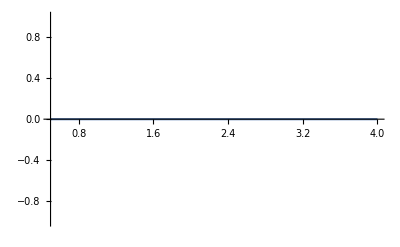

```mathematica
Plot[Abs[BarnesG[1+2 2+2x]BarnesG[1-2 2-2 x]]/BarnesG[1+2 2+2x]^2 Abs[(π/(I Sin [2π 2]))^(-2 x)BarnesG[1+2 x]/BarnesG[1-2 x]],{x,1/2,4}]
```

```mathematica
Sin[2π(1/2+x)]//Simplify
```

-Sin[2 π x]

```mathematica
Log[-I]
```

-(ⅈ π)/2

```mathematica
2Log[(π/(I Sin[2 π x]))]//Simplify
```

2 Log[-ⅈ π Csc[2 π x]]

```mathematica
2Log[(π/(I Sin[2 π x]))]/.x->1/2+x//Simplify
```

2 Log[ⅈ π Csc[2 π x]]

```mathematica
(G[1+2x]/G[1-2x])^2/((G[1+2x]/G[1-2x])^2/.x->1/2+x)//Cancel
```

1/(4 x^2 Γ[-2 x]^2 Γ[2 x]^2)

```mathematica
Plot[ Abs[(π/(I Sin 2π x))^(2 2)],{x,1/2,1}]
```

-Graphics-

```mathematica
1/(1-σ1+σ2)^2(Simplify[(Subscript[F, 0][-1+σ1,σ2] Subscript[F, 0][σ1,1+σ2])/(Subscript[F, 0][-1+σ1,1+σ2] Subscript[F, 0][σ1,σ2])/. Subscript[F, 0][σ1_,σ2_]->(1/(G[1-σ1+σ2]G[1+σ1-σ2])/.{σ1->I σ1,σ2->I σ2, σ3-> I σ3, σ4-> I σ4})]//Cancel)
```

(G[-2 ⅈ+ⅈ (σ1-σ2)] G[ⅈ σ1-ⅈ σ2] G[-ⅈ σ1+ⅈ σ2] G[2 ⅈ-ⅈ σ1+ⅈ σ2] Γ[-2 ⅈ+ⅈ (σ1-σ2)] Γ[ⅈ σ1-ⅈ σ2] Γ[-ⅈ σ1+ⅈ σ2] Γ[2 ⅈ-ⅈ σ1+ⅈ σ2])/((1-σ1+σ2)^2 G[-ⅈ+ⅈ (σ1-σ2)]^2 G[ⅈ-ⅈ σ1+ⅈ σ2]^2 Γ[-ⅈ+ⅈ (σ1-σ2)]^2 Γ[ⅈ-ⅈ σ1+ⅈ σ2]^2)

```mathematica
1/(1+x)^2(Simplify[(Subscript[F, 0][1+x] Subscript[F, 0][1+x])/(Subscript[F, 0][2+x] Subscript[F, 0][x])/. Subscript[F, 0][σ1_]->1/(G[1- σ1]G[ 1-σ1])]//Cancel)
```

1

```mathematica
Exp[]
```

```mathematica
Series[(BarnesG[-ⅈ-ⅈ x] BarnesG[ⅈ-ⅈ x]BarnesG[ⅈ+ⅈ x] BarnesG[3 ⅈ+ⅈ x])/((1+x)^2 BarnesG[2 ⅈ+ⅈ x]^2 BarnesG[-ⅈ x]^2),{x,Infinity,0}]
```

1/(BarnesG[-ⅈ-ⅈ x]^2 BarnesG[ⅈ+ⅈ x]^2)2^(2 Floor[1/2+Arg[-ⅈ-ⅈ x]/(2 π)]-Floor[1/2+Arg[-2 ⅈ-ⅈ x]/(2 π)]+2 Floor[1/2+Arg[ⅈ+ⅈ x]/(2 π)]-Floor[1/2+Arg[2 ⅈ+ⅈ x]/(2 π)]) BarnesG[-2 ⅈ-ⅈ x] BarnesG[2 ⅈ+ⅈ x] BarnesG[-ⅈ x] BarnesG[ⅈ x] Csc[-ⅈ π x-ⅈ π+O[1/x]^5]^(-2 Floor[1/2+Arg[-ⅈ-ⅈ x]/(2 π)]) Csc[-ⅈ π x-2 ⅈ π+O[1/x]^5]^Floor[1/2+Arg[-2 ⅈ-ⅈ x]/(2 π)] Csc[ⅈ π x+ⅈ π+O[1/x]^5]^(-2 Floor[1/2+Arg[ⅈ+ⅈ x]/(2 π)]) Csc[ⅈ π x+2 ⅈ π+O[1/x]^5]^Floor[1/2+Arg[2 ⅈ+ⅈ x]/(2 π)] O[1/x]^2

```mathematica
Plot[(BarnesG[-ⅈ-ⅈ x] BarnesG[ⅈ-ⅈ x]BarnesG[ⅈ+ⅈ x] BarnesG[3 ⅈ+ⅈ x])/((1+x)^2 BarnesG[2 ⅈ+ⅈ x]^2 BarnesG[-ⅈ x]^2),{x,3,5}]
```

-Graphics-

```mathematica
Simplify[(Subscript[F, 0][-1+σ1,σ2,σ3,σ4] Subscript[F, 0][σ1,σ2,σ3,1+σ4])/((1-σ1+σ4)^2 Subscript[F, 0][-1+σ1,σ2,σ3,1+σ4] Subscript[F, 0][σ1,σ2,σ3,σ4])/. Subscript[F, 0][σ1_,σ2_,σ3_,σ4_]->ⅇ^(+1/2 ⅈ π (3 σ1^2+3 σ2^2+3 σ3^2-2 σ3 σ4+3 σ4^2-2 σ2 (σ3+σ4)-2 σ1 (σ2+σ3+σ4)))/(G[1-σ1+σ2]G[1+σ1-σ2]G[1-σ1+σ3]G[1+σ1-σ3]G[1-σ1+σ4]G[1+σ1-σ4]G[1-σ2+σ3]G[1+σ2-σ3]G[1-σ2+σ4]G[1+σ2-σ4]G[1-σ4+σ3]G[1+σ4-σ3]),{σ1 >0, σ2 >0, σ3 >0,σ4>0}]
```

1

```mathematica
Exp[1/2I π(σ1-σ2)^2]G[1-σ1+σ2]G[1+σ1-σ2]Exp[1/2I π(σ1-σ3)^2]G[1-σ1+σ3]G[1+σ1-σ3]Exp[1/2I π(σ1-σ4)^2]G[1-σ1+σ4]G[1+σ1-σ4]Exp[1/2I π(σ2-σ3)^2]G[1-σ2+σ3]G[1+σ2-σ3]Exp[1/2I π(σ2-σ4)^2]G[1-σ2+σ4]G[1+σ2-σ4]Exp[1/2I π(σ4-σ3)^2]G[1-σ4+σ3]G[1+σ4-σ3]//Simplify
```

ⅇ^(1/2 ⅈ π (3 σ1^2+3 σ2^2+3 σ3^2-2 σ3 σ4+3 σ4^2-2 σ2 (σ3+σ4)-2 σ1 (σ2+σ3+σ4))) G[σ1-σ2] G[-σ1+σ2] G[σ1-σ3] G[σ2-σ3] G[-σ1+σ3] G[-σ2+σ3] G[σ1-σ4] G[σ2-σ4] G[σ3-σ4] G[-σ1+σ4] G[-σ2+σ4] G[-σ3+σ4] Γ[σ1-σ2] Γ[-σ1+σ2] Γ[σ1-σ3] Γ[σ2-σ3] Γ[-σ1+σ3] Γ[-σ2+σ3] Γ[σ1-σ4] Γ[σ2-σ4] Γ[σ3-σ4] Γ[-σ1+σ4] Γ[-σ2+σ4] Γ[-σ3+σ4]

```mathematica
Expand[(3 σ1^2+3 σ2^2+3 σ3^2-2 σ3 σ4+3 σ4^2-2 σ2 (σ3+σ4)-2 σ1 (σ2+σ3+σ4))/.σ4->-σ1-σ2-σ3]
```

8 σ1^2+8 σ1 σ2+8 σ2^2+8 σ1 σ3+8 σ2 σ3+8 σ3^2

```mathematica
Simplify[8 σ1^2+8 σ1 σ2+8 σ2^2+8 σ1 σ3+8 σ2 σ3+8 σ3^2]
```

8 (σ1^2+σ2^2+σ2 σ3+σ3^2+σ1 (σ2+σ3))

```mathematica
Product[Exp[1/4I π (a.{σ1,σ2,σ3,σ4,σ5,σ6,σ6,σ6})^2],{a,E6Roots}]//Simplify
```

ⅇ^(6 ⅈ π (σ1^2+σ2^2+σ3^2+σ4^2+σ5^2+3 σ6^2))

```mathematica
D3RootList = Flatten[Table[If[(a^2+b^2+c^2==2),{a,b,c},Nothing],{a,-1,1},{b,-1,1},{c,-1,1}],2];
```

```mathematica
Product[Exp[-1/2I π (a.{σ1,σ2,σ3})^2],{a,D3RootList}]//Simplify
```

ⅇ^(-4 ⅈ π (σ1^2+σ2^2+σ3^2))

```mathematica
B3RootList = Join[D3RootList,Flatten[Table[If[(a^2+b^2+c^2==1),{a,b,c},Nothing],{a,-1,1},{b,-1,1},{c,-1,1}],2]];
```

```mathematica
Product[Exp[-1/2I π (a.{σ1,σ2,σ3})^2],{a,B3RootList}]//Simplify
```

ⅇ^(-5 ⅈ π (σ1^2+σ2^2+σ3^2))

```mathematica
A3RootList = Flatten[Table[If[a+b+c+d==0&&(a^2+b^2+c^2+d^2==2),{a,b,c,d},Nothing],{a,-1,1},{b,-1,1},{c,-1,1},{d,-1,1}],3];
Product[Exp[1/4I π (a.{σ1,σ2,σ3,σ4})^2],{a,A3RootList}]//Simplify
```

ⅇ^(1/2 ⅈ π (3 σ1^2+3 σ2^2+3 σ3^2-2 σ3 σ4+3 σ4^2-2 σ2 (σ3+σ4)-2 σ1 (σ2+σ3+σ4)))

```mathematica
C3RootList = Join[D3RootList,Flatten[2Table[If[(a^2+b^2+c^2==1),{a,b,c},Nothing],{a,-1,1},{b,-1,1},{c,-1,1}],2]];
Product[Exp[-1/2I π (a.{σ1,σ2,σ3})^2],{a,C3RootList}]//Simplify
```

ⅇ^(-8 ⅈ π (σ1^2+σ2^2+σ3^2))

```mathematica
F4ShortRootList1 = Flatten[Table[If[(a^2+b^2+c^2+d^2==1),{a,b,c,d},Nothing],{a,-1,1},{b,-1,1},{c,-1,1},{d,-1,1}],3];
F4ShortRootList2 = Flatten[Table[{a,b,c,d},{a,-1/2,1/2,1},{b,-1/2,1/2,1},{c,-1/2,1/2,1},{d,-1/2,1/2,1}],3]//DeleteDuplicates;
F4LongRootList = Flatten[Table[If[a^2+b^2+c^2+d^2==2,{a,b,c,d},Nothing],{a,-2,2},{b,-2,2},{c,-2,2},{d,-2,2}],3];
F4RootList = Join[F4LongRootList,F4ShortRootList1,F4ShortRootList2];
Product[Exp[-1/2I π (a.{σ1,σ2,σ3,σ4})^2],{a,F4RootList}]//Simplify
```

ⅇ^(-9 ⅈ π (σ1^2+σ2^2+σ3^2+σ4^2))

```mathematica
A1RootList = Flatten[Table[If[a+b==0&&(a^2+b^2==2),{a,b},Nothing],{a,-1,1},{b,-1,1}],1];
Product[Exp[1/4I π (a.{σ1,σ2})^2],{a,A1RootList}]//Simplify
```

ⅇ^(1/2 ⅈ π (σ1-σ2)^2)

```mathematica
(ⅇ^(1/2 ⅈ π (σ1-σ2)^2)/.{σ1->σ1+n1+1,σ2->-σ1-n1})/(ⅇ^(1/2 ⅈ π (σ1-σ2)^2)/.{σ1->σ1,σ2->-σ1})(ⅇ^(1/2 ⅈ π (σ1-σ2)^2)/.{σ1->σ1+m1+1,σ2->-σ1-m1})/(ⅇ^(1/2 ⅈ π (σ1-σ2)^2)/.{σ1->σ1,σ2->-σ1})//Simplify
```

ⅇ^(ⅈ π (1+2 m1^2+2 n1^2+4 σ1+m1 (2+4 σ1)+n1 (2+4 σ1)))

```mathematica
ⅈ π (1+2 m1^2+2 n1^2+4 σ1+m1 (2+4 σ1)+n1 (2+4 σ1))//Expand
```

ⅈ π+2 ⅈ m1 π+2 ⅈ m1^2 π+2 ⅈ n1 π+2 ⅈ n1^2 π+4 ⅈ π σ1+4 ⅈ m1 π σ1+4 ⅈ n1 π σ1

```mathematica
ⅇ^(1/2 ⅈ π (1+2n1+2σ1)^2)ⅇ^(1/2 ⅈ π (1+2n1+2σ1)^2)//ApartSquareFree
```

```mathematica
-ⅈ π (1+2 n1+2 σ1)^2//Expand
```

-ⅈ π-4 ⅈ n1 π-4 ⅈ n1^2 π-4 ⅈ π σ1-8 ⅈ n1 π σ1-4 ⅈ π σ1^2

```mathematica
(ⅇ^(1/2 ⅈ π (3 σ1^2+3 σ2^2+3 σ3^2-2 σ3 σ4+3 σ4^2-2 σ2 (σ3+σ4)-2 σ1 (σ2+σ3+σ4)))/.{σ1->σ1+n1+1,σ2->σ2+n2,σ3->σ3+n3})/(ⅇ^(1/2 ⅈ π (3 σ1^2+3 σ2^2+3 σ3^2-2 σ3 σ4+3 σ4^2-2 σ2 (σ3+σ4)-2 σ1 (σ2+σ3+σ4))))(ⅇ^(1/2 ⅈ π (3 σ1^2+3 σ2^2+3 σ3^2-2 σ3 σ4+3 σ4^2-2 σ2 (σ3+σ4)-2 σ1 (σ2+σ3+σ4)))/.{σ1->σ1+m1-1,σ2->σ2+m2,σ3->σ3+m3})/(ⅇ^(1/2 ⅈ π (3 σ1^2+3 σ2^2+3 σ3^2-2 σ3 σ4+3 σ4^2-2 σ2 (σ3+σ4)-2 σ1 (σ2+σ3+σ4))))//Simplify
```

ⅇ^(-1/2 ⅈ π (6 σ1^2-3 (-1+m1+σ1)^2-3 (1+n1+σ1)^2+6 σ2^2-3 (m2+σ2)^2-3 (n2+σ2)^2+6 σ3^2-3 (m3+σ3)^2-3 (n3+σ3)^2-4 σ3 σ4+2 (m3+σ3) σ4+2 (n3+σ3) σ4-4 σ2 (σ3+σ4)+2 (m2+σ2) (m3+σ3+σ4)+2 (n2+σ2) (n3+σ3+σ4)-4 σ1 (σ2+σ3+σ4)+2 (-1+m1+σ1) (m2+m3+σ2+σ3+σ4)+2 (1+n1+σ1) (n2+n3+σ2+σ3+σ4)))

```mathematica
Coefficient[-1/2 ⅈ π (6 σ1^2-3 (-1+m1+σ1)^2-3 (1+n1+σ1)^2+6 σ2^2-3 (m2+σ2)^2-3 (n2+σ2)^2+6 σ3^2-3 (m3+σ3)^2-3 (n3+σ3)^2-4 σ3 σ4+2 (m3+σ3) σ4+2 (n3+σ3) σ4-4 σ2 (σ3+σ4)+2 (m2+σ2) (m3+σ3+σ4)+2 (n2+σ2) (n3+σ3+σ4)-4 σ1 (σ2+σ3+σ4)+2 (-1+m1+σ1) (m2+m3+σ2+σ3+σ4)+2 (1+n1+σ1) (n2+n3+σ2+σ3+σ4)),σ1,0]
```

-1/2 ⅈ π (-6+6 m1-3 m1^2-2 m2+2 m1 m2-3 m2^2-2 m3+2 m1 m3+2 m2 m3-3 m3^2-6 n1-3 n1^2+2 n2+2 n1 n2-3 n2^2+2 n3+2 n1 n3+2 n2 n3-3 n3^2+2 m1 σ2-6 m2 σ2+2 m3 σ2+2 n1 σ2-6 n2 σ2+2 n3 σ2+2 m1 σ3+2 m2 σ3-6 m3 σ3+2 n1 σ3+2 n2 σ3-6 n3 σ3+2 m1 σ4+2 m2 σ4+2 m3 σ4+2 n1 σ4+2 n2 σ4+2 n3 σ4)

```mathematica
Tau[]
```

```mathematica
F[x+1]F[x-1]/F[x]^2/.F[x_]->1/(G[1+2x]G[1-2x])//Simplify
```

1/(16 x^4 (1-4 x^2)^2)

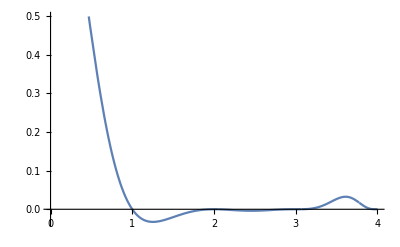

```mathematica
Plot[(BarnesG[1+x]BarnesG[1-x])/(BarnesG[1+I x]BarnesG[1-I x])(BarnesG[]/□),{x,0,4}]
```

```mathematica
FullSimplify[(Series[Log[BarnesG[1+x]],{x,Infinity,4}]//Normal),{x>0,x ϵ Reals}]
```

1/12+(5-21 (x^2+180 x^6))/(5040 x^4)-Log[Glaisher]+1/2 x Log[2 π]+1/12 (-1+6 x^2) Log[x]

```mathematica
(5-21 (x^2+180 x^6))/(5040 x^4)//Expand
```

1/(1008 x^4)-1/(240 x^2)-(3 x^2)/4

```mathematica
1/12-(3 x^2)/4-Log[Glaisher]+1/2 x Log[2 π]+1/12 (-1+6 x^2) Log[x]/.{x->I x}
```

```mathematica
1/12+(3 x^2)/4-Log[Glaisher]+1/2 ⅈ x Log[2 π]+1/12 (-1-6 x^2)(Log[x]+Log[I] )
```

1/12+(3 x^2)/4-Log[Glaisher]+1/2 ⅈ x Log[2 π]+1/12 (-1-6 x^2) ((ⅈ π)/2+Log[x])

```mathematica
1/12-(3 x^2)/4-Log[Glaisher]+1/2 x Log[2 π]+1/12 (-1+6 x^2) Log[x]/.{x->-I x}
```

1/12+(3 x^2)/4-Log[Glaisher]-1/2 ⅈ x Log[2 π]+1/12 (-1-6 x^2) Log[-ⅈ x]

```mathematica
1/12+(3 x^2)/4-Log[Glaisher]-1/2 ⅈ x Log[2 π]+1/12 (-1-6 x^2)(Log[x]+Log[-I])
```

1/12+(3 x^2)/4-Log[Glaisher]-1/2 ⅈ x Log[2 π]+1/12 (-1-6 x^2) (-(ⅈ π)/2+Log[x])

```mathematica
1/12+(3 x^2)/4-Log[Glaisher]-1/2 ⅈ x Log[2 π]+1/12 (-1-6 x^2) (-(ⅈ π)/2+Log[x])+1/12+(3 x^2)/4-Log[Glaisher]+1/2 ⅈ x Log[2 π]+1/12 (-1-6 x^2) ((ⅈ π)/2+Log[x])
```

1/6+(3 x^2)/2-2 Log[Glaisher]+1/12 (-1-6 x^2) (-(ⅈ π)/2+Log[x])+1/12 (-1-6 x^2) ((ⅈ π)/2+Log[x])

```mathematica
Cancel[1/6+(3 x^2)/2-2 Log[Glaisher]+1/12 (-1-6 x^2) (-(ⅈ π)/2+Log[x])+1/12 (-1-6 x^2) ((ⅈ π)/2+Log[x])]
```

1/6+(3 x^2)/2-2 Log[Glaisher]-1/24 ⅈ (1+6 x^2) (π-2 ⅈ Log[x])+1/24 ⅈ (1+6 x^2) (π+2 ⅈ Log[x])

```mathematica
Simplify[1/6+(3 x^2)/2-2 Log[Glaisher]-1/24 ⅈ (1+6 x^2) (π-2 ⅈ Log[x])+1/24 ⅈ (1+6 x^2) (π+2 ⅈ Log[x])]//Expand
```

1/6+(3 x^2)/2-2 Log[Glaisher]-Log[x]/6-x^2 Log[x]